# Quantum Mechanics

## A derivation of the fundamental equations of Schrodinger’s quantum mechanics

```mathematica
(* ALSO DO INFINITE SQUARE WELL*)


(* ALSO DO TUNELLING THROUGH A STEP *)
```

```mathematica
(* for psi = |psi|^(i phase(psi), probability current: j(r) ~ |psi(r)|^2 gradient(phase(r))... for ANY quantum wavef.
for BEC, then simplifies to a superfluid velocity of ~grad(phase) *)
```

```mathematica
(* use DYNAMIC to change plots based on coeffs *)
```

```mathematica
(* TODO: REPLACE DSOLVE WITH DSOLVEVALUE *)
(* TODO: normalisation is expensive and pointless *)
```

### draft outline

ya:
- Born interpretation

- correspondence rules (with dimensional analysis)
- Hamiltonian
- t.d. Schrodinger equation
- stationary states (t.i Schrod)
- e.g. harmonic oscillator states
- coherent states

nah:
- deriv wave equ
- deriv Schrod from wav
- On hilbert space -> space mechanics
- GPE
- BdG

```mathematica
ClearAll["Global`*"]
```

```mathematica
<< Notation`
Symbolize[Ĥ]
Symbolize[K̂]
Symbolize[V̂]
Symbolize[P̂]
Symbolize[Schrod]
Symbolize[Subscript[ϕ, osc]]
```

## The Schro^(..)dinger Equation

The time-dependent Schrodinger equation describes the evolution of the quantum wavefunction ψ, for a system with total energy given by the Hamiltonian Ĥ.

```mathematica
Schrod[ψ_] :=  
	ⅈ ℏ D[ψ, t] == Ĥ[ψ]
Schrod[ψ[t]]
```

ⅈ ℏ ψ'[t]==Ĥ[ψ[t]]

We’ll assume the particular form of the Hamiltonian is time-independent.

```mathematica
Ĥ[c_ ψ_] := c Ĥ[ ψ ]   /;   D[c, r]==0
```

By substituting the wavefunction for an eigenfunction of the Hamiltonian...

```mathematica
Schrod[ψ[r, t]] /. Ĥ[ψ[r, t]] ->  Energy ψ[r, t]
```

ⅈ ℏ ψ^(0,1)[r,t]==Energy ψ[r,t]

we can realise the temporal form of the energy eigenfunctions in terms of a time-independent wavefunction ϕ...

```mathematica
ψeigsub = DSolve[%, ψ[r, t], {r, t}][[1]][[1]]  /. C[1] -> ϕ
{%, Derivative[0,1][ψ][r,t]-> D[ψ[r, t] /. %, t]} ;
```

ψ[r,t]→ⅇ^(-(ⅈ Energy t)/ℏ) ϕ[r]

which when substituted back into the Schrodinger equation...

```mathematica
Schrod[ ψ[r, t] ] /. %
```

ⅇ^(-(ⅈ Energy t)/ℏ) Energy ϕ[r]==ⅇ^(-(ⅈ Energy t)/ℏ) Ĥ[ϕ[r]]

presents an equation for the time-independent eigenfunctions

```mathematica
SchrodTI  = Simplify[%, Energy >0]
```

Ĥ[ϕ[r]]==Energy ϕ[r]

## The Correspondence rules

```mathematica
Quantity[x, "kilograms"] Quantity[F, "newtons"] // FullSimplify
```

F x kg N

```mathematica
(* TODO *)
```

```mathematica
P̂[ψ_] := -ⅈ ℏ D[ψ, r]
```

```mathematica
K̂[ψ_] := (P̂[ P̂[ψ]])/(2m)
```

```mathematica
(*    V̂[ψ_] := 1/2 m ω^2 r^2           just a scalar potential quantity! *)
```

```mathematica
Ĥ[ψ_] := K̂[ψ] + V̂[ψ]
```

```mathematica
Ĥ[ψ[r]]
```

V̂[ψ[r]]-(ℏ^2 ψ''[r])/(2 m)

## The Quantum Harmonic Oscillator

```mathematica
assumps = {m > 0, ω >0, ℏ > 0};
naturalunits = {m -> 1, ω -> 1, ℏ -> 1};
```

A 1D harmonic trap, parametrized by the natural frequency ω, has a potential

```mathematica
V̂[ψ_] := 1/2 m ω^2 r^2 ψ
```

The time-independent Schrodinger equation then becomes

```mathematica
SchrodTI
```

1/2 m r^2 ω^2 ϕ[r]-(ℏ^2 ϕ''[r])/(2 m)==Energy ϕ[r]

which we can solve for the time-independent energy eigenfunctions ϕ[r] and their eigenvalues Energy

```mathematica
DSolve[SchrodTI, ϕ[r], r]  // Flatten
```

{ϕ[r]→C[2] ParabolicCylinderD[(-2 Energy-ω ℏ)/(2 ω ℏ),(ⅈ √2 √m r √ω)/(√ℏ)]+C[1] ParabolicCylinderD[(2 Energy-ω ℏ)/(2 ω ℏ),(√2 √m r √ω)/(√ℏ)]}

With two arbitrary constants (and one normalisation condition), we’ll arbitrarily set C[2] to 0, which presents a real basis.

```mathematica
Subscript[ϕ, osc][r] =  ϕ[r] /. FunctionExpand[Simplify[% , {Energy > 0  , C[2] == 0}] ]
```

2^(1/2 (1/2-Energy/(ω ℏ))) ⅇ^(-(m r^2 ω)/(2 ℏ)) C[1] HermiteH[-1/2+Energy/(ω ℏ),(√m r √ω)/(√ℏ)]

Enforcing the Hermite polynomials have integer order...

```mathematica
n ==Extract[ Subscript[ϕ, osc][r],  Position[Subscript[ϕ, osc][r], _HermiteH] // Flatten ][[1]]
```

n==-1/2+Energy/(ω ℏ)

lets us solve for the energy eigenvalue spectrum, parameterized by quantum number n...

```mathematica
Ensub = Solve[%, Energy] // Flatten
```

{Energy→1/2 (1+2 n) ω ℏ}

which gives our energy eigenfunctions parameterized by n as

```mathematica
ϕ[r, n_] = Subscript[ϕ, osc][r] /. % //FullSimplify
```

2^(-n/2) ⅇ^(-(m r^2 ω)/(2 ℏ)) C[1] HermiteH[n,(√m r √ω)/(√ℏ)]

Our arbitrary complex constant is resolved with the normalisation condition ∫|ψ|^2 dr = 1; Mathematica will arbitrarily choose real values, and we’ll arbitrarily choose the positive one

```mathematica
numModes = 5;
TIcoeffs = Table[ 
{
      Solve[
         Integrate[
          Abs[ϕ[r,n1]]^2, {r, -∞, ∞},  
          Assumptions ->  assumps] == 1,
         C[1]][[2]] [[1]],
    n -> n1
},
    {n1, 0,numModes-1}]
```

{{C[1]→(m ω ℏ)^(1/4)/(π^(1/4) √ℏ),n→0},{C[1]→(√m √ω (ℏ/(m ω))^(1/4))/(π^(1/4) √ℏ),n→1},{C[1]→(√m √ω (ℏ/(m ω))^(1/4))/(√2 π^(1/4) √ℏ),n→2},{C[1]→(m ω ℏ)^(1/4)/(√6 π^(1/4) √ℏ),n→3},{C[1]→(√m √ω (ℏ/(m ω))^(1/4))/(2 √6 π^(1/4) √ℏ),n→4}}

We now know the analytic energy eigenfunctions to an arbitrary phase

```mathematica
eigfuncs[r_] = ϕ[r, n] /. TIcoeffs // FullSimplify[#, Assumptions -> assumps] &
```

{(ⅇ^(-(m r^2 ω)/(2 ℏ)) ((m ω)/ℏ)^(1/4))/π^(1/4),(√2 ⅇ^(-(m r^2 ω)/(2 ℏ)) r ((m ω)/ℏ)^(3/4))/π^(1/4),(ⅇ^(-(m r^2 ω)/(2 ℏ)) (2 m r^2 ω-ℏ) (m ω ℏ)^(1/4))/(√2 π^(1/4) ℏ^(3/2)),(ⅇ^(-(m r^2 ω)/(2 ℏ)) r (m ω)^(3/4) (2 m r^2 ω-3 ℏ))/(√3 π^(1/4) ℏ^(7/4)),(ⅇ^(-(m r^2 ω)/(2 ℏ)) (m ω ℏ)^(1/4) (4 m^2 r^4 ω^2-12 m r^2 ω ℏ+3 ℏ^2))/(2 √6 π^(1/4) ℏ^(5/2))}

here plotted as a real eigenbasis (subset)

```mathematica
plotfuncs
```

plotfuncs

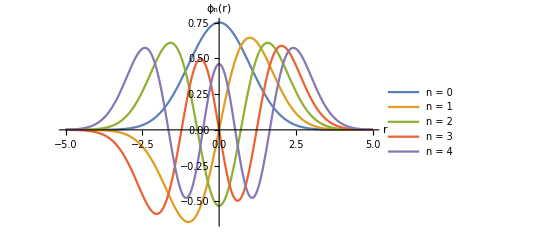

```mathematica
plotfuncs = eigfuncs[r]/. naturalunits;
Plot[ 
plotfuncs,  {r, -5, 5}, 
AxesLabel -> {r, Subscript[ϕ, n][r] },
PlotRange -> All, PlotLegends-> Map["n = " <> ToString[ #] &, Range[0, numModes-1]]
]
```

Each eigenfunction is “static”; their corresponding time-dependent wavefunctions merely oscillate in complex phase at a rate proportional to their energy (there is no phase gradient to induce motion via the Laplacian)

```mathematica
(* use doubles instead of ints for speedup <> precision loss *)
```

```mathematica
(* don't use delayed assigns; get expressions for speedup *)
```

```mathematica
plotwaves[t_] = ψ[r, t] /. ψeigsub /. Ensub  /. ϕ[r] -> ϕ[r, n] /. TIcoeffs /. naturalunits
```

{(ⅇ^(-r^2/2-(ⅈ t)/2))/π^(1/4),(√2 ⅇ^(-r^2/2-(3 ⅈ t)/2) r)/π^(1/4),(ⅇ^(-r^2/2-(5 ⅈ t)/2) (-2+4 r^2))/(2 √2 π^(1/4)),(ⅇ^(-r^2/2-(7 ⅈ t)/2) (-12 r+8 r^3))/(4 √3 π^(1/4)),(ⅇ^(-r^2/2-(9 ⅈ t)/2) (12-48 r^2+16 r^4))/(8 √6 π^(1/4))}

```mathematica
(* consider Compiling this function *)
```

```mathematica
colorfunc[r1_, t_, n_] := Hue[Arg[plotwaves[t][[n+1]]] / π /. r -> r1]     (* pi <> 2pi *)
```

```mathematica
Manipulate[
      Animate[
          Plot[
             Abs[plotwaves[t][[n+1]] ]^2 , 
             {r, -5, 5}, 
             Filling -> Axis, ColorFunction-> Function[x, colorfunc[x, t, n]] ,
             AxesLabel -> {r, Norm[Subscript[ϕ, n][r]]^2 }      
             (* PlotLegends-> BarLegend[{Hue, {0, 2π}},
                                                              "Ticks" -> {0, 1.0*π, 1.99*π},
                              "TickLabels" -> {0, π, 2π}] *)
             ],
       {t, 0, 2 π}],
       {n, 0, numModes-1, 1}
]
```

```mathematica
(* TODO: fix colorbar slowdown *)
(* TODO: fix slow af shitty design *)
```

Since the Schrodinger equation (or more intuitively, the unitary time-evolution operator) is linear, all dynamics of the quantum harmonic oscillator can be decomposed into a superposition of those of individual time-dependent eigenfunctions...

```mathematica
superpos[r_, t_] = 
 Total[
    Table[ 
        C[n] plotwaves[t][[n]], {n, 1, numModes}]]
```

(ⅇ^(-r^2/2-(ⅈ t)/2) C[1])/π^(1/4)+(√2 ⅇ^(-r^2/2-(3 ⅈ t)/2) r C[2])/π^(1/4)+(ⅇ^(-r^2/2-(5 ⅈ t)/2) (-2+4 r^2) C[3])/(2 √2 π^(1/4))+(ⅇ^(-r^2/2-(7 ⅈ t)/2) (-12 r+8 r^3) C[4])/(4 √3 π^(1/4))+(ⅇ^(-r^2/2-(9 ⅈ t)/2) (12-48 r^2+16 r^4) C[5])/(8 √6 π^(1/4))

weighted by their complex amplitudes in the initial wavefunction,

```mathematica
coeffs = Table[C[n] -> 0, {n,  numModes}];
```

```mathematica
setCoeff[sub_] := coeffs = coeffs /. {(sub[[1]] -> _) -> (sub)}
```

```mathematica
setCoeffs[subs_] :=  (setCoeff[#]&) /@ subs
```

```mathematica
setCoeffs[{  
C[1] -> 3ⅈ, 
C[3] -> 0,
C[5] -> 6  ,
C[6] -> Exp[ 3 π ⅈ/2]
}];
```

and which must be globally normalised, to maintain the Born interpretation.

```mathematica
superwave[r_, t_] = 
With[
	{norm = √Integrate[ Abs[(superpos[r1, 0] /. coeffs)]^2, {r1, -∞, ∞}]},
         superpos[r, t] /norm /. coeffs // FullSimplify
]
```

(ⅇ^(1/2 (-r^2-9 ⅈ t)) (6 ⅈ ⅇ^(4 ⅈ t)+√6 (3+4 r^2 (-3+r^2))))/(6 √5 π^(1/4))

```mathematica
superprob[r_, t_] := Abs[superwave[r, t]]^2    (* may need to be = for speed *)
```

Different phase rates between the eigenfunctions (proportional to their energies) ,sees a (in general, inhomogeneous) phase gradient across the superposition, corresponding to kinetic energy and producing “motion” of the probability distribution

```mathematica
superphase[r_, t_] := Arg[superpos[r, t] /. coeffs]
```

```mathematica
Animate[
     Plot[
        superprob[r, t], 
        {r, -5, 5},
         AxesLabel -> {r, Norm[ψ[r,"t"]]^2 }, Filling -> Axis,
         PlotRange -> {0, 1 },(*1.05*FindMaximum[ superprob[r1, t1], {r1, t1}][[1]]}, *)
         ColorFunction->  Function[{x}, Hue[ superphase[x, t] / π]]
         (*
          PlotLegends-> BarLegend[{Hue, {0, 2π}},
                                                           "Ticks" -> {0, 1.0*π, 1.99*π},
                                                           "TickLabels" -> {0, π, 2π}]
     *)
    ],
      {t, 0, 2π}
]
```

```mathematica
(* TODO: fix max val *)
(* TOOD: fix colorbar slowdown *)
(* TODO: add dotted profiles of individual eig prob densities*** (is this actually insightful?)
          NO: it's not insightful because of normalisation; you'd need to fudge the norm *)
(* TODO add label of coeffs of eigenmodes *)
```

Coherent states are careful superpositions of the entire eigenbasis with a translating (but otherwise fixed) probability profile.

## Scratch

```mathematica
(* doesn't seem to scale the Jacobian; what gives *)
(* http://functions.wolfram.com/Polynomials/HermiteH/21/01/02/02/0001/ *)
(* arg[HermiteH] *= c *)
```

```mathematica
Integrate[ Exp[- r^2]  HermiteH[n, c r], r,  Assumptions -> {n  ∈ Integers, n ≥ 0}  ]
```

Integrate[ⅇ^(-r^2) HermiteH[n,c r],r,Assumptions→{n∈Integers,n≥0}]

```mathematica
Integrate[ⅇ^(-r^2) HermiteH[n, r],r,Assumptions->{n∈Integers,n≥0}]
```

2^n √π ((r HypergeometricPFQ[{1/2+n/2},{3/2},-r^2])/Gamma[(1-n)/2]+(-1+HypergeometricPFQ[{n/2},{1/2},-r^2])/(n Gamma[-n/2]))